Part::pkspec1: The expression x cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{2.82597,3.9988}

{1.40386,1.599}

{2.36744,1.00019}

{1.90242,3.90065}

{3.99428,2.98657}

{3.99771,2.72806}

{1.00465,2.04292}

{1.01025,2.98977}

{1.03277,1.97616}

{3.82155,1.82619}

{1.44964,3.44951}

{3.75872,3.71003}

{3.84224,3.47248}

{3.79384,3.61484}

{2.05629,3.99263}

{1.00262,2.1105}

{2.05018,1.00072}

{3.99691,2.11728}

{3.99853,2.59927}

{3.01693,3.98977}

{3.9963,2.8844}

{3.17267,1.17451}

{1.00149,2.92138}

{1.89237,1.10818}

{1.00124,2.42709}

{2.79347,1.00196}

{2.86205,1.00859}

{3.23123,3.92156}

{1.00081,2.53239}

{2.12221,3.99959}

{1.94892,3.94126}

{3.90965,3.26762}

{1.01388,3.01271}

{3.03364,1.04235}

{3.74246,3.7357}

{3.99571,2.02754}

{3.99113,3.01293}

{3.97989,1.98526}

{1.98498,1.0172}

{2.96662,1.02637}

{1.27342,3.27309}

{3.70923,3.75966}

Part::pkspec1: The expression x cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{6.99987,2.65702}

{2.00125,5.05262}

{6.09701,6.99724}

{2.00009,6.01992}

{5.06745,2.00216}

{6.99892,2.35403}

{2.00734,6.98673}

{4.06504,6.99985}

{6.82802,2.00409}

{6.9829,2.14564}

{6.88602,2.00813}

{2.02477,5.02335}

{4.88031,6.99949}

{5.92209,6.99791}

{5.0178,2.01209}

{2.44312,6.99913}

{6.92691,2.02655}

{6.99447,2.25009}

{6.99583,6.98671}

{6.99908,6.90402}

{6.96292,2.0707}

{6.13594,2.00093}

{6.98712,6.99347}

{{3.70923,3.75966},{1.27342,3.27309},{2.96662,1.02637},{1.98498,1.0172},{3.97989,1.98526},{3.99113,3.01293},{3.99571,2.02754},{3.74246,3.7357},{3.03364,1.04235},{1.01388,3.01271},{3.90965,3.26762},{1.94892,3.94126},{2.12221,3.99959},{1.00081,2.53239},{3.23123,3.92156},{2.86205,1.00859},{2.79347,1.00196},{1.00124,2.42709},{1.89237,1.10818},{1.00149,2.92138},{3.17267,1.17451},{3.9963,2.8844},{3.01693,3.98977},{3.99853,2.59927},{3.99691,2.11728},{2.05018,1.00072},{1.00262,2.1105},{2.05629,3.99263},{3.79384,3.61484},{3.84224,3.47248},{3.75872,3.71003},{1.44964,3.44951},{3.82155,1.82619},{1.03277,1.97616},{1.01025,2.98977},{1.00465,2.04292},{3.99771,2.72806},{3.99428,2.98657},{1.90242,3.90065},{2.36744,1.00019},{1.40386,1.599},{2.82597,3.9988}}

{{6.98712,6.99347},{6.13594,2.00093},{6.96292,2.0707},{6.99908,6.90402},{6.99583,6.98671},{6.99447,2.25009},{6.92691,2.02655},{2.44312,6.99913},{5.0178,2.01209},{5.92209,6.99791},{4.88031,6.99949},{2.02477,5.02335},{6.88602,2.00813},{6.9829,2.14564},{6.82802,2.00409},{4.06504,6.99985},{2.00734,6.98673},{6.99892,2.35403},{5.06745,2.00216},{2.00009,6.01992},{6.09701,6.99724},{2.00125,5.05262},{6.99987,2.65702}}

Nejbližší pár bodů hledaných na konvexní obálce: {{3.99571,2.02754},{5.0178,2.01209}}

Vysílající pár: {{3.99571,2.02754},{3.97989,1.98526}}

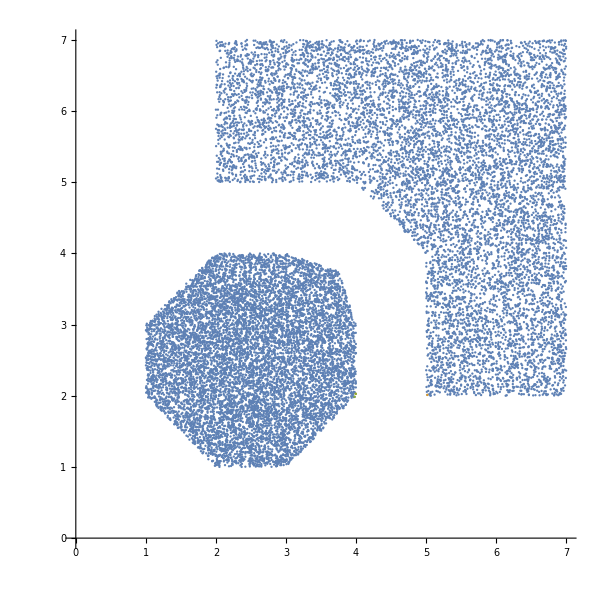

Nejbližší pár bodů ze všech bodů: {{2.82597,3.9988},{2.80239,5.00129}}

Vysílající pár: {{2.82597,3.9988},{2.81403,3.99694}}

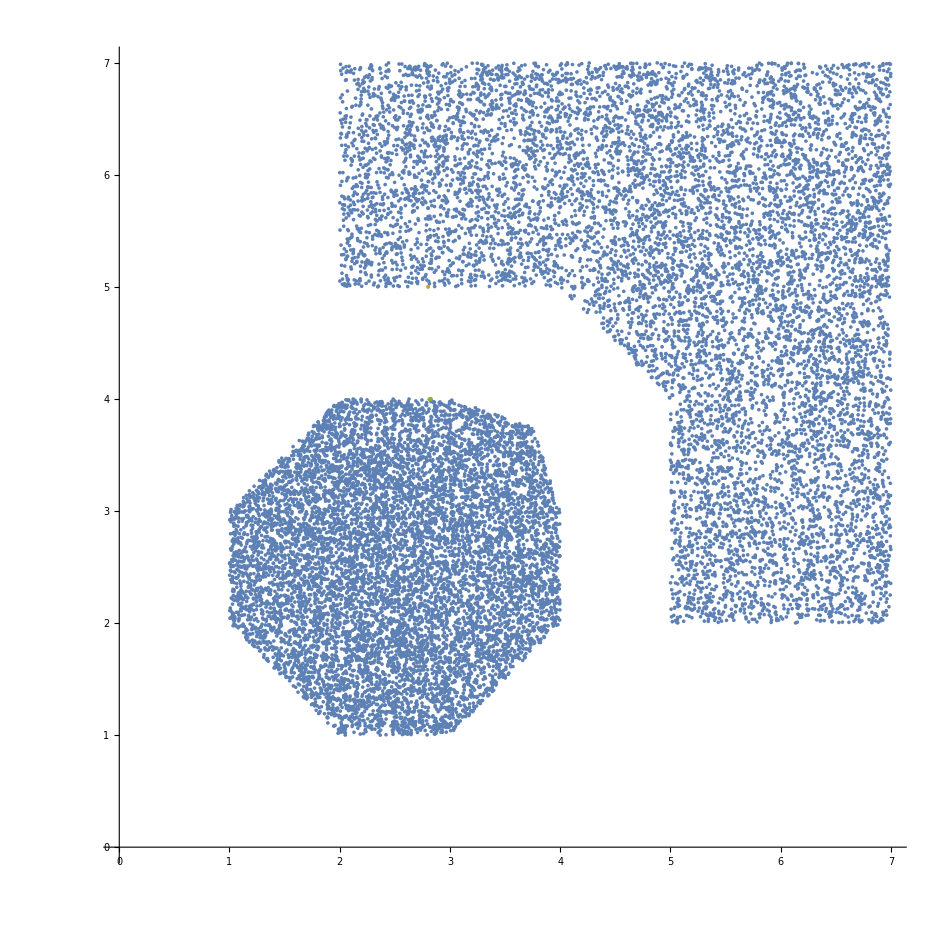

Pouze v jedné oblastni se nachází nejbližší bod na konvexní obálce, v druhé ne.

Pouze jeden z vysílačů se nachází na konvexní obálce

```mathematica
(*Global Variables*)
numOfPoints = 10000;

(*Distributin function for generating point on given region*)
RegionDistribution/:
Random`DistributionVector[RegionDistribution[reg_MeshRegion],n_Integer,prec_?Positive]:=Module[{d=RegionDimension@reg,cells,measures,s,m},cells=Developer`ToPackedArray@MeshPrimitives[reg,d][[All,1]];
s=RandomVariate[DirichletDistribution@ConstantArray[1,d+1],n];
measures=PropertyValue[{reg,d},MeshCellMeasure];
m=RandomVariate[#,n]&@EmpiricalDistribution[measures->Range@Length@cells];
#[[All,1]] (1-Total[s,{2}])+Total[#[[All,2;;]] s,{2}]&@cells[[m]]]

(*(*Initialize of two RECTANGLE regions*)
region1 = DiscretizeRegion@Rectangle[{0,1},{3,4}];
region2 = DiscretizeRegion@Rectangle[{2,6},{12,12}];*)

(*(*Initialize of two CIRCLE regions*)
region1 = DiscretizeRegion@Disk[{10,10}, 10];
region2 = DiscretizeRegion@Disk[{30,30}, 10];*)

(*Initialize of two POLYGON regions*)
region1 = DiscretizeRegion@Polygon[{{2,1},{3,1},{4,2},{4,3},{3.75, 3.75}, {3, 4}, {2, 4}, {1, 3}, {1, 2}}];
region2 = DiscretizeRegion@Polygon[{{5,2}, {7,2}, {7,7}, {2,7}, {2, 5}, {4, 5}, {5, 4}}];

pts1= RandomVariate[RegionDistribution[region1],numOfPoints];
pts2= RandomVariate[RegionDistribution[region2],numOfPoints];
area = Join[pts1, pts2];

(*Exctract points on convex hull - both regions*)
convexHullpts1 = RegionBoundary[ConvexHullMesh[pts1]];
convexHullpts2 = RegionBoundary[ConvexHullMesh[pts2]];

arrayOneConvexHull = pts1;
cutConvexHull1[x_]=If[RegionMember[convexHullpts1,arrayOneConvexHull[[x]]],Print[arrayOneConvexHull[[x]]], arrayOneConvexHull = Delete[arrayOneConvexHull, x]];
For[i=numOfPoints, i>0, i--, cutConvexHull1[i]];

arrayTwoConvexHull = pts2;
cutConvexHull2[x_]=If[RegionMember[convexHullpts2,arrayTwoConvexHull[[x]]],Print[arrayTwoConvexHull[[x]]], arrayTwoConvexHull = Delete[arrayTwoConvexHull, x]];
For[i=numOfPoints, i>0, i--, cutConvexHull2[i]];

arrayOneConvexHull
arrayTwoConvexHull

(*Calculate nearest on ConvexHull*)
f = Nearest[arrayOneConvexHull];
c=Flatten[f/@arrayTwoConvexHull,1];
closestPairOnConvexHull = Flatten[Transpose[{c[[#]],arrayTwoConvexHull[[#]]}]&@Ordering[Norm/@(c-arrayTwoConvexHull),1],1];
Print["Nejbližší pár bodů hledaných na konvexní obálce: ", closestPairOnConvexHull]
transmittersOnConvexHull = Nearest[arrayOneConvexHull,closestPairOnConvexHull[[1]],{2,5}];
Print["Vysílající pár: ", transmittersOnConvexHull]
ListPlot[{area, closestPairOnConvexHull, transmittersOnConvexHull}, AspectRatio->Automatic]

(*Calculate nearest point of two regions*)
r = Nearest[pts1];
d = Flatten[r/@pts2,1];
closestPair = Flatten[Transpose[{d[[#]],pts2[[#]]}]&@Ordering[Norm/@(d-pts2),1],1];
Print["Nejbližší pár bodů ze všech bodů: ", closestPair]
transmitters = Nearest[pts1,closestPair[[1]],{2,5}];
Print["Vysílající pár: ", transmitters]
ListPlot[{area, closestPair, transmitters}, AspectRatio->Automatic]

(*Check if points are the same and if they belong to convex hull*)
If[closestPair == closestPairOnConvexHull,
Print["Nejbližší body z obou oblastní jsou na konvexní obálce - Nezáleží na tom zda vyhledáváme pouze na obálce nebo ze všech"],
(*Else*)If[(ContainsAny[arrayOneConvexHull, closestPair])&&(ContainsAny[arrayTwoConvexHull, closestPair]),Print["Nejbližší body z obou oblastní jsou na konvexní obálce - Při hladání ze všech prvků jsme dostali menší vzdálenost"], 
(*Else*)If[(ContainsAny[arrayOneConvexHull, closestPair])||(ContainsAny[arrayTwoConvexHull, closestPair]),
Print["Pouze v jedné oblastni se nachází nejbližší bod na konvexní obálce, v druhé ne. "],
(*Else*)Print["Ani jeden z bodů se nenachází na konvexní obálce"]]]]

(*Check if are both transmiters on convex hull*)
If[(ContainsAny[arrayOneConvexHull, transmitters])&&(ContainsAny[arrayTwoConvexHull, transmitters]),
Print["Oba vysílače se nachází na konvexní obálce"], 
(*Else*)If[(ContainsAny[arrayOneConvexHull, transmitters])||(ContainsAny[arrayTwoConvexHull, transmitters]),
Print["Pouze jeden z vysílačů se nachází na konvexní obálce"],
(*Else*)Print["Ani jeden z vysílačů se nenachází na konvexní obálce"]]]
```